```mathematica
AX = B
a = Table[RandomInteger[{-10,10}],{i, 5}, {j, 5}]; 
Print[a//MatrixForm];
b = {6,10,13,31,4};
```

B

(-5 | 8 | 7 | 8 | -2
10 | 0 | 10 | -4 | 3
-9 | 7 | -4 | -3 | 2
-3 | 2 | 9 | 0 | 0
-7 | 6 | -3 | 0 | 7)

```mathematica
Det[a]
```

-61112

```mathematica
b = a.{-2,-1,0,1,2}
```

{6,-18,12,4,22}

```mathematica
Inverse[a].b
```

{-2,-1,0,1,2}

```mathematica
LinearSolve[a, b]
```

```mathematica
{-2,-1,0,1,2}

LinearSolve[{1,2,3}, {7,8,9}];
```

{-2,-1,0,1,2}

LinearSolve::matrix: Argument {1,2,3} at position 1 is not a non-empty rectangular matrix.

```mathematica
Solve[x x-20x+244== 0,x]
```

{{x→10-12 ⅈ},{x→10+12 ⅈ}}

```mathematica
Solve[{x x x - 2x == y, x y-y^2==-6-x}, {x,y}]
```

{{x→2,y→4},{x→Root-1.92Root[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,1]-1.9151452015298034,y→Root-1.92Root[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,1]-1.9151452015298034 (-2+(Root-1.92Root[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,1]-1.9151452015298034)^2)},{x→Root-0.979-0.512 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,2]-0.97884904590426,y→Root-0.979-0.512 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,2]-0.97884904590426 (-2+(Root-0.979-0.512 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,2]-0.97884904590426)^2)},{x→Root-0.979+0.512 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,3]-0.97884904590426,y→Root-0.979+0.512 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,3]-0.97884904590426 (-2+(Root-0.979+0.512 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,3]-0.97884904590426)^2)},{x→Root0.936-0.638 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,4]0.9364216466691617,y→Root0.936-0.638 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,4]0.9364216466691617 (-2+(Root0.936-0.638 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,4]0.9364216466691617)^2)},{x→Root0.936+0.638 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,5]0.9364216466691617,y→Root0.936+0.638 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,5]0.9364216466691617 (-2+(Root0.936+0.638 ⅈRoot[3+2 #1-2 #1^2-#1^3+2 #1^4+#1^5&,5]0.9364216466691617)^2)}}

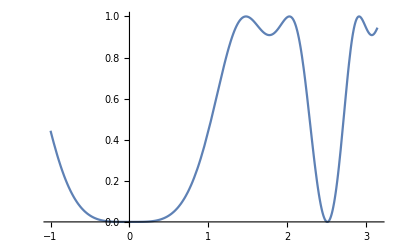

```mathematica
Plot[Sin[1-Cos[x x]], {x, -1, Pi}, PlotStyle->{Green, Thick}]
```

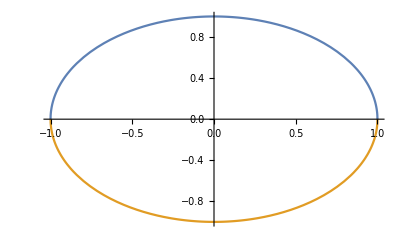

```mathematica
Plot[{√(1 - w w), -√(1 - w w)}, {w, -1,1}]
```

```mathematica
t = Table[(i^3-5i)/(1+i!),{i,0,6,.5}]
```

{0.,-1.25913,-2.,-1.77089,-0.666667,0.722819,1.71429,2.00883,1.76,1.28649,0.826446,0.480727,0.257975}

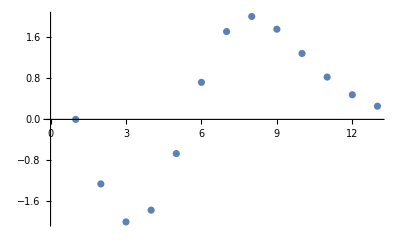

```mathematica
ListPlot[t]
```

```mathematica
Plot3D[E^Sin[(-x x - y y)], {x,-π, π}, {y,-π, π}]
```

-Graphics3D-